```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
metalvl4={Real,Real,Real,Real,Real,Real,Real,Real};
metalvl4={Real,Real,Real,Real,Real,Real,Real,Real,Real};
st=0;end=20000;int=200;endy=60;minus=20;Ω0=2Pi/(86164);
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

## E: Here we plot E_B*<tf>/ts and take the average of all runs. This is an alternative method to Tau-Histograms and they have to agree within 1.1%.

Run 10 #: 12693

Run 10 #: 12695

Run 10 #: 12697

Run 10 #: 12704

Run 10 #: 12707

Run 10 #: 12771

Run 10 #: 12775

Run 10 #: 12778

Run 10 #: 12779

Run 10 #: 12780

Run 20 #: 13102

Run 20 #: 13104

Run 20 #: 13106

Run 20 #: 13107

Run 20 #: 13133

Run 20 #: 13138

Run 20 #: 13142

Run 20 #: 13146

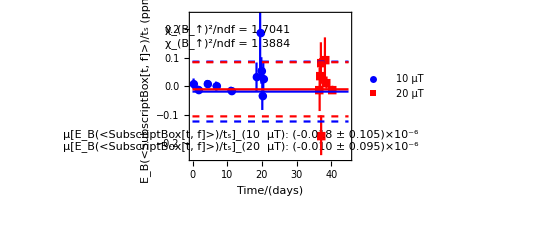

```mathematica
lvl4={};
lvl4={};
tsadd=PlusMinus[11.306,0.397];
sttime=0;
pttstfe10={};fttstfe10={};errtstfe10={};
pttstfet10={};fttstfet10={};errtstfet10={};
pttstfe20={};fttstfe20={};errtstfe20={};
pttstfet20={};fttstfet20={};errtstfet20={};
For[i=1,i≤dimdesc,i++,
If[i==1,sttime=lvl4[[1]][[1]]];
If[(descdat[[i]][[6]]==10)(*separating B fields, indicating 10 muT*)
,
Print["Run 10 #: ",descdat[[i]][[4]]];(*separating B fields, indicating 10 muT*)
lvl4=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl4.dat"],metalvl4];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(*
pttstfe10=AppendTo[pttstfe10,{{ts[[1]],ts[[2]]},{lvl4[[1]][[3]],lvl4[[1]][[4]]}*(descdat[[i]][[9]]/ts[[1]])}];
fttstfe10=AppendTo[fttstfe10,{ts[[1]],lvl4[[1]][[3]]}*(descdat[[i]][[9]]/ts[[1]])];
errtstfe10=AppendTo[errtstfe10,lvl4[[1]][[2]]*(descdat[[i]][[9]]/ts[[1]])];
*)
pttstfet10=AppendTo[pttstfet10,{xx,{lvl4[[1]][[3]],lvl4[[1]][[4]]}*(descdat[[i]][[9]]/ts[[1]])}];
fttstfet10=AppendTo[fttstfet10,{xx,lvl4[[1]][[3]]}*(descdat[[i]][[9]]/ts[[1]])];
errtstfet10=AppendTo[errtstfet10,lvl4[[1]][[4]]*(descdat[[i]][[9]]/ts[[1]])];
];
If[(descdat[[i]][[6]]==20)(*separating B fields, indicating 10 muT*)
,
Print["Run 20 #: ",descdat[[i]][[4]]];(*separating B fields, indicating 20 muT*)
lvl4=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl4.dat"],metalvl4];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(*
pttstfe20=AppendTo[pttstfe20,{{ts[[1]],ts[[2]]},{lvl4[[1]][[3]],lvl4[[1]][[4]]}*(descdat[[i]][[9]]/ts[[1]])}];
fttstfe20=AppendTo[fttstfe20,{ts[[1]],lvl4[[1]][[3]]}*(descdat[[i]][[9]]/ts[[1]])];
errtstfe20=AppendTo[errtstfe20,lvl4[[1]][[4]]*(descdat[[i]][[9]]/ts[[1]])];
*)
pttstfet20=AppendTo[pttstfet20,{xx,{lvl4[[1]][[3]],lvl4[[1]][[4]]}*(descdat[[i]][[9]]/ts[[1]])}];
fttstfet20=AppendTo[fttstfet20,{xx,lvl4[[1]][[3]]}*(descdat[[i]][[9]]/ts[[1]])];
errtstfet20=AppendTo[errtstfet20,lvl4[[1]][[4]]*(descdat[[i]][[9]]/ts[[1]])];
];
]
xx=((Abs[-lvl4[[1]][[1]]+lvl4[[2]][[1]]]/2)+Abs[lvl4[[1]][[1]]-sttime])/(86164);(*Time where 0=first cycle of mirror neutron run, 86164s = sidereal day*)
nlm10=Mean[WeightedData[fttstfet10],m x + c,{m,c},x,Weights->errtstfet10];
(*Calculating chi^2, error on central value, mean, width of distrubution*)
ftval10={m/.nlm10["BestFitParameters"],c/.nlm10["BestFitParameters"]};
fterr10=nlm10["ParameterErrors"];
ftresidue10=nlm10["FitResiduals"];
nlm10["ParameterTable"]
nlm10["ANOVATable"]
1+nlm10["EstimatedVariance"]
ndim10=Dimensions[fttstfet10][[1]];
Print["χ2_10: ",(∑_(i=1)^ndim10 (pttstfet10[[i]][[2]][[1]]/pttstfet10[[i]][[2]][[2]])^2)/(ndim10-1)]
(*20*)
nlm20=Mean[WeightedData[fttstfet20],m x + c,{m,c},x,Weights->errtstfet20];
(*Calculating chi^2, error on central value, mean, width of distrubution*)
ftval20={m/.nlm20["BestFitParameters"],c/.nlm20["BestFitParameters"]};
fterr20=nlm20["ParameterErrors"];
ftresidue20=nlm20["FitResiduals"];
nlm20["ParameterTable"]
nlm20["ANOVATable"]
1+nlm20["EstimatedVariance"]
ndim20=Dimensions[fttstfet20][[1]];
Print["χ2_20: ",(∑_(i=1)^ndim20 (pttstfet20[[i]][[2]][[1]]/pttstfet20[[i]][[2]][[2]])^2)/(ndim20-1)]
(*Plotting distrubution, time series, width of the distribution, error on mean, mean
Note: Edited=Chi^2 to be actual χ^2*)
Show[{
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,45},{-.25,.25}},PlotLegends->{"10 μT","20 μT"},Frame->True,FrameLabel->{"Time/(days)","E_B(<SubscriptBox[t, f]>)/t_s (ppm)"},PlotStyle->{Blue,Red},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
Epilog->{
Text[Style["χ_(B_↑)^2/ndf = ",χ2_10,FontSize->Large],{10,.15}],
Text[Style["χ_(B_↑)^2/ndf =",χ2_20,FontSize->Large],{10,.2}],
Text[Style["μ[E_B(<SubscriptBox[t, f]>)/t_s]_(10  μT):","μ[E_B(<SubscriptBox[t, f]>)/t_s]_(20  μT)",FontSize->Large],{14,-.19}]
},PlotMarkers->{Automatic,Medium}
],
}]
```

```mathematica
Print[tau[[eb10,;;,;;]]](*Only 0-field limits have numbers, the rest come with scaling factor, for B'≠ 0*)
(*Separated limits, 10muT: 90%, 95%, 99%*)
```

2425.11

2033.18

1554.2

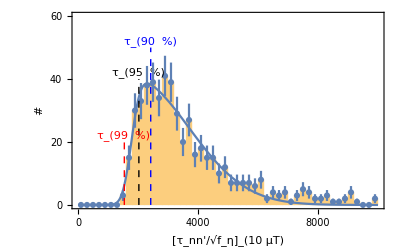

```mathematica
Show[{
Histogram[Sqrt[Select[1/eb10,#>0&]],{st,end,int}, Frame->True,FrameLabel->{"[τ_nn'/√f_η]_(10  μT)","#"},Axes->False,PlotRange->{{st,end},{0,endy}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{2424-minus,52}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{2029-minus,42}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{1544-minus,22}],Large]}}],
EDAListPlot[datpt],
Plot[{fit[x]},{x,st,end},PlotRange->{{st,end},{0,endy}}]
},ImageSize->{800}]
```

```mathematica
Print[tau[[eb20,;;,;;]]](*Only 0-field limits have numbers, the rest come with scaling factor, for B'≠ 0*)
(*Separated limits, 10muT: 90%, 95%, 99%*)
```

2544.09

2112.

1602.46

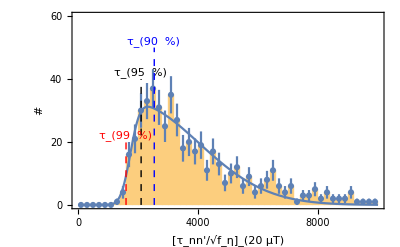

```mathematica
Show[{
Histogram[Sqrt[Select[1/eb20,#>0&]],{st,end,int}, Frame->True,FrameLabel->{"[τ_nn'/√f_η]_(20  μT)","#"},Axes->False,PlotRange->{{st,end},{0,endy}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{2542-minus,52}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{2104-minus,42}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{1601-minus,22}],Large]}}],
EDAListPlot[datpt],
Plot[{fit[x]},{x,st,end},PlotRange->{{st,end},{0,endy}}]
},ImageSize->{800}]
```

## A: Here we plot A_B*<tf>/ts and take the average of all runs. This is an alternative method to Tau-Histograms and they have to agree within 1.1%.

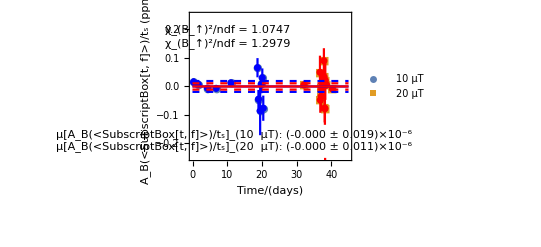

```mathematica
lvl4={};
lvl4={};
tsadd=PlusMinus[11.306,0.397];
sttime=0;
pttstfe10={};fttstfe10={};errtstfe10={};
pttstfet10={};fttstfet10={};errtstfet10={};
pttstfe20={};fttstfe20={};errtstfe20={};
pttstfet20={};fttstfet20={};errtstfet20={};
For[i=1,i≤dimdesc,i++,
lvl4=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl4.dat"],metalvl4];
If[i==1,sttime=lvl4[[1]][[1]]];
If[(descdat[[i]][[6]]==10)(*separating B fields, indicating 10 muT*)
,
(*Print["Run 10 #: ",descdat[[i]][[4]]];*)(*separating B fields, indicating 10 muT*)
lvl4=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl4.dat"],metalvl4];
(*
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
pttstfe10=AppendTo[pttstfe10,{{ts[[1]],ts[[2]]},{lvl4[[1]][[1]],lvl4[[1]][[2]]}*(descdat[[i]][[9]]/ts[[1]])}];
fttstfe10=AppendTo[fttstfe10,{ts[[1]],lvl4[[1]][[1]]}*(descdat[[i]][[9]]/ts[[1]])];
errtstfe10=AppendTo[errtstfe10,lvl4[[1]][[2]]*(descdat[[i]][[9]]/ts[[1]])];
*)
pttstfet10=AppendTo[pttstfet10,{xx,{lvl4[[1]][[1]],lvl4[[1]][[2]]}*(descdat[[i]][[9]]/ts[[1]])}];
fttstfet10=AppendTo[fttstfet10,{xx,lvl4[[1]][[1]]}*(descdat[[i]][[9]]/ts[[1]])];
errtstfet10=AppendTo[errtstfet10,lvl4[[1]][[2]]*(descdat[[i]][[9]]/ts[[1]])];
];
If[(descdat[[i]][[6]]==20)(*separating B fields, indicating 20 muT*)
,
(*Print["Run 20 #: ",descdat[[i]][[4]]];*)(*separating B fields, indicating 20 muT*)
lvl4=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl4.dat"],metalvl4];
(*
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
pttstfe20=AppendTo[pttstfe20,{{ts[[1]],ts[[2]]},{lvl4[[1]][[1]],lvl4[[1]][[2]]}*(descdat[[i]][[9]]/ts[[1]])}];
fttstfe20=AppendTo[fttstfe20,{ts[[1]],lvl4[[1]][[1]]}*(descdat[[i]][[9]]/ts[[1]])];
errtstfe20=AppendTo[errtstfe20,lvl4[[1]][[2]]*(descdat[[i]][[9]]/ts[[1]])];
*)
pttstfet20=AppendTo[pttstfet20,{xx,{lvl4[[1]][[1]],lvl4[[1]][[2]]}*(descdat[[i]][[9]]/ts[[1]])}];
fttstfet20=AppendTo[fttstfet20,{xx,lvl4[[1]][[1]]}*(descdat[[i]][[9]]/ts[[1]])];
errtstfet20=AppendTo[errtstfet20,lvl4[[1]][[2]]*(descdat[[i]][[9]]/ts[[1]])];
];
]
xx=((Abs[-lvl4[[1]][[1]]+lvl4[[-1]][[1]]]/2)+Abs[lvl4[[1]][[1]]-sttime])/(86164);
nlm10=Mean[WeightedData[fttstfet10],m x + c,{m,c},x,Weights->errtstfet10];
(*Calculating chi^2, error on central value, mean, width of distrubution*)
ftval10={m/.nlm10["BestFitParameters"],c/.nlm10["BestFitParameters"]};
fterr10=nlm10["ParameterErrors"];
ftresidue10=nlm10["FitResiduals"];
nlm10["ParameterTable"]
nlm10["ANOVATable"]
1+nlm10["EstimatedVariance"]
ndim10=Dimensions[fttstfet10][[1]];
Print["χ2_10: ",(∑_(i=1)^ndim10 (pttstfet10[[i]][[2]][[1]]/pttstfet10[[i]][[2]][[2]])^2)/(ndim10-1)]
(*20*)
nlm20=Mean[WeightedData[fttstfet20],m x + c,{m,c},x,Weights->errtstfet20];
(*Calculating chi^2, error on central value, mean, width of distrubution*)
ftval20={m/.nlm20["BestFitParameters"],c/.nlm20["BestFitParameters"]};
fterr20=nlm20["ParameterErrors"];
ftresidue20=nlm20["FitResiduals"];
nlm20["ParameterTable"]
nlm20["ANOVATable"]
1+nlm20["EstimatedVariance"]
ndim20=Dimensions[fttstfet20][[1]];
Print["χ2_20: ",(∑_(i=1)^ndim20 (pttstfet20[[i]][[2]][[1]]/pttstfet20[[i]][[2]][[2]])^2)/(ndim20-1)]
(*Plotting distrubution, time series, width of the distribution, error on mean, mean*)
Show[{
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,45},{-.25,.25}},PlotLegends->{"10 μT","20 μT"},Frame->True,FrameLabel->{"Time/(days)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
Epilog->{
Text[Style["χ_(B_↑)^2/ndf = ",χ2_10,FontSize->Large],{10,.15}],
Text[Style["χ_(B_↑)^2/ndf =",χ2_20,FontSize->Large],{10,.2}],
Text[Style["μ[E_B(<SubscriptBox[t, f]>)/t_s]_(10  μT):","μ[E_B(<SubscriptBox[t, f]>)/t_s]_(20  μT)",FontSize->Large],{14,-.19}]
},PlotMarkers->{Automatic,Medium}]
}]
```

```mathematica
Print[tau[[ab10,;;,;;]]](*Only 0-field limits have numbers, the rest come with scaling factor, for B'≠ 0*)
(*Separated limits, 10muT: 90%, 95%, 99%*)
```

5733.76

4803.01

3655.11

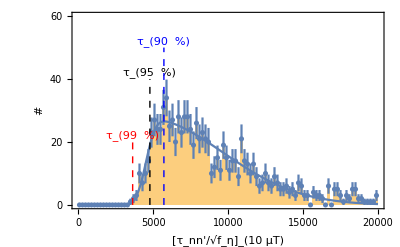

```mathematica
Show[{
Histogram[Sqrt[Select[1/ab10,#>0&]],{st,end,int}, Frame->True,FrameLabel->{"[τ_nn'/√f_η]_(10  μT)","#"},Axes->False,PlotRange->{{st,end},{0,endy}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{5727-minus,52}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{4793-minus,42}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{3644-minus,22}],Large]}}],
EDAListPlot[datpt],
Plot[{fit[x]},{x,st,end},PlotRange->{{st,end},{0,endy}}]
},ImageSize->{800}]
```

```mathematica
Print[tau[[ab20,;;,;;]]](*Only 0-field limits have numbers, the rest come with scaling factor, for B'≠ 0*)
(*Separated limits, 20muT: 90%, 95%, 99%*)
```

7403.45

6191.76

4711.

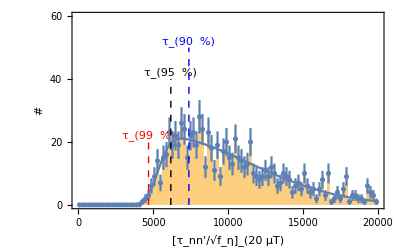

```mathematica
Show[{
Histogram[Sqrt[Select[1/ab20,#>0&]],{st,end,int}, Frame->True,FrameLabel->{"[τ_nn'/√f_η]_(20  μT)","#"},Axes->False,PlotRange->{{st,end},{0,endy}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{7393-minus,52}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{6188-minus,42}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{4703-minus,22}],Large]}}],
EDAListPlot[datpt],
Plot[{fit[x]},{x,st,end},PlotRange->{{st,end},{0,endy}}]
},ImageSize->{800}]
```

## Sidereal Modulation

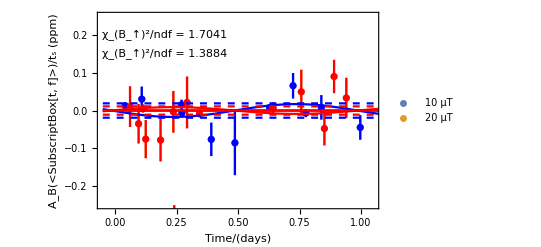

```mathematica
lvl4={};
lvl4={};
tsadd=PlusMinus[11.306,0.397];
sttime=0;
pttstfe10={};fttstfe10={};errtstfe10={};
pttstfet10={};fttstfet10={};errtstfet10={};
pttstfe20={};fttstfe20={};errtstfe20={};
pttstfet20={};fttstfet20={};errtstfet20={};
For[i=1,i≤dimdesc,i++,
lvl4=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl4.dat"],metalvl4];
If[i==1,sttime=lvl4[[1]][[1]]];
xx=Mod[((Abs[-lvl4[[1]][[1]]+lvl4[[-1]][[1]]]/2)+Abs[lvl4[[1]][[1]]-sttime])/(86164),1];(*Here we take the Modulo sidereal day, this way it is also easier to show a 1wavelet fitted cos wave, and the plot shows only 1 day as x-axis*)
If[(descdat[[i]][[6]]==10)(*separating B fields, indicating 10 muT*)
,
(*Print["Run 10 #: ",descdat[[i]][[4]]];*)(*separating B fields, indicating 10 muT*)
lvl4=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl4.dat"],metalvl4];
(*
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
pttstfe10=AppendTo[pttstfe10,{{ts[[1]],ts[[2]]},{lvl4[[1]][[1]],lvl4[[1]][[2]]}*(descdat[[i]][[9]]/ts[[1]])}];
fttstfe10=AppendTo[fttstfe10,{ts[[1]],lvl4[[1]][[1]]}*(descdat[[i]][[9]]/ts[[1]])];
errtstfe10=AppendTo[errtstfe10,lvl4[[1]][[2]]*(descdat[[i]][[9]]/ts[[1]])];
*)
pttstfet10=AppendTo[pttstfet10,{xx,{lvl4[[1]][[1]],lvl4[[1]][[2]]}*(descdat[[i]][[9]]/ts[[1]])}];
fttstfet10=AppendTo[fttstfet10,{xx,lvl4[[1]][[1]]}*(descdat[[i]][[9]]/ts[[1]])];
errtstfet10=AppendTo[errtstfet10,lvl4[[1]][[2]]*(descdat[[i]][[9]]/ts[[1]])];
];
If[(descdat[[i]][[6]]==20)(*separating B fields, indicating 20 muT*)
,
(*Print["Run 20 #: ",descdat[[i]][[4]]];*)(*separating B fields, indicating 20 muT*)
lvl4=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl4.dat"],metalvl4];
(*ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
pttstfe20=AppendTo[pttstfe20,{{ts[[1]],ts[[2]]},{lvl4[[1]][[1]],lvl4[[1]][[2]]}*(descdat[[i]][[9]]/ts[[1]])}];
fttstfe20=AppendTo[fttstfe20,{ts[[1]],lvl4[[1]][[1]]}*(descdat[[i]][[9]]/ts[[1]])];
errtstfe20=AppendTo[errtstfe20,lvl4[[1]][[2]]*(descdat[[i]][[9]]/ts[[1]])];
*)
pttstfet20=AppendTo[pttstfet20,{xx,{lvl4[[1]][[1]],lvl4[[1]][[2]]}*(descdat[[i]][[9]]/ts[[1]])}];
fttstfet20=AppendTo[fttstfet20,{xx,lvl4[[1]][[1]]}*(descdat[[i]][[9]]/ts[[1]])];
errtstfet20=AppendTo[errtstfet20,lvl4[[1]][[2]]*(descdat[[i]][[9]]/ts[[1]])];
];
]
(*nlm10=Mean[WeightedData[fttstfet10],m x + c,{m,c},x,Weights->errtstfet10];, this is not used here, but same from old*)
nlmcos10=Mean[WeightedData[fttstfet10],m Cos[Ω0 x+c]+a,{m,c,a},x,Weights->errtstfet10];
ftval10={m/.nlmcos10["BestFitParameters"],c/.nlmcos10["BestFitParameters"],a/.nlmcos10["BestFitParameters"]};
fterr10=nlmcos10["ParameterErrors"];
ftresidue10=nlmcos10["FitResiduals"];
nlmcos10["ParameterTable"]
nlmcos10["ANOVATable"]
1+nlmcos10["EstimatedVariance"]
ndim10=Dimensions[fttstfet10][[1]];
Print["χ2_10: ",(∑_(i=1)^ndim10 (pttstfet10[[i]][[2]][[1]]/pttstfet10[[i]][[2]][[2]])^2)/(ndim10-1)]
(*20*)
nlmcos20=Mean[WeightedData[fttstfet20],m Cos[Ω0 x+c]+a,{m,c,a},x,Weights->errtstfet20];
ftval20={m/.nlmcos20["BestFitParameters"],c/.nlmcos20["BestFitParameters"],,a/.nlmcos20["BestFitParameters"]};
fterr20=nlmcos20["ParameterErrors"];
ftresidue20=nlmcos20["FitResiduals"];
nlmcos20["ParameterTable"]
nlmcos20["ANOVATable"]
1+nlmcos20["EstimatedVariance"]
ndim20=Dimensions[fttstfet20][[1]];
Print["χ2_20: ",(∑_(i=1)^ndim20 (pttstfet20[[i]][[2]][[1]]/pttstfet20[[i]][[2]][[2]])^2)/(ndim20-1)]
Show[{
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,1.05},{-.25,.25}},PlotLegends->{"10 μT","20 μT"},Frame->True,FrameLabel->{"Time/(days)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
Epilog->{
Text[Style["χ_(B_↑)^2/ndf = ",χ2_10,FontSize->Large],{10,.15}],
Text[Style["χ_(B_↑)^2/ndf =",χ2_20,FontSize->Large],{10,.2}],
Text[Style["μ[E_B(<SubscriptBox[t, f]>)/t_s]_(10  μT):","μ[E_B(<SubscriptBox[t, f]>)/t_s]_(20  μT)",FontSize->Large],{14,-.19}]
}
],
}]
```

```mathematica
Print[tau[[abcos10,;;,;;]]](*Only 0-field limits have numbers, the rest come with scaling factor, for B'≠ 0*)
(*Separated limits, 10muT: 90%, 95%, 99%*)
```

1611.16

1358.71

1029.22

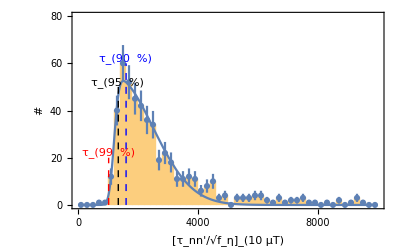
```mathematica
Show[{
Histogram[Sqrt[Select[1/abcos10,#>0&]],{st,end,int}, Frame->True,FrameLabel->{"[τ_nn'/√f_η]_(10  μT)","#"},Axes->False,PlotRange->{{st,end},{0,endy}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{1603-minus,62}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{1343-minus,52}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{1022-minus,22}],Large]}}],
EDAListPlot[datpt],
Plot[{fit[x]},{x,st,end},PlotRange->{{st,end},{0,endy}}]
},ImageSize->{800}]
-Graphics-
```

```mathematica
Print[tau[[abcos20,;;,;;]]](*Only 0-field limits have numbers, the rest come with scaling factor, for B'≠ 0*)
(*Separated limits, 20muT: 90%, 95%, 99%*)
```

2544.56

2130.65

1620.58

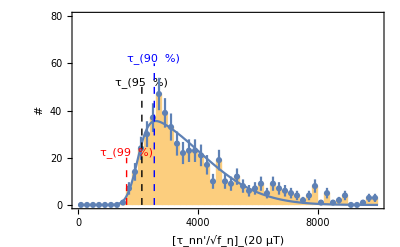

```mathematica
Show[{
Histogram[Sqrt[Select[1/ebcos20,#>0&]],{st,end,int}, Frame->True,FrameLabel->{"[τ_nn'/√f_η]_(20  μT)","#"},Axes->False,PlotRange->{{st,end},{0,endy}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{2543-minus,62}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{2129-minus,52}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{1620-minus,22}],Large]}}],
EDAListPlot[datpt],
Plot[{fit[x]},{x,st,end},PlotRange->{{st,end},{0,endy}}]
},ImageSize->{800}]
```